```mathematica
ClearAll["Global`*"]
```

## AA 279C - PSet 2 - Ellipsoids

```mathematica
tvec={1,2,-2};
lvec={1,2,-1};
ivec={1,2,0};
wvec={0,0,-1};

2wvec+ivec-tvec
2wvec+2ivec-2lvec
```

{0,0,0}

{0,0,0}

```mathematica
bpidim={tvec,lvec,ivec,wvec}ᵀ;
bpidim//MatrixForm
MatrixRank[bpidim]
RowReduce[bpidim]//MatrixForm
NullSpace[bpidim] //MatrixForm
bpidim.NullSpace[bpidim] [[1]]
bpidim.NullSpace[bpidim] [[2]]

pi1vec={-1,0,1,2};
pi2vec={0,-2,2,2};
bpidim.pi1vec
bpidim.pi2vec
```

(1 | 1 | 1 | 0
2 | 2 | 2 | 0
-2 | -1 | 0 | -1)

2

(1 | 0 | -1 | 1
0 | 1 | 2 | -1
0 | 0 | 0 | 0)

(-1 | 1 | 0 | 1
1 | -2 | 1 | 0)

{0,0,0}

{0,0,0}

{0,0,0}

«1 more identical outputs»

```mathematica
pi1primevec=pi1vec-2pi2vec
pi2primevec=pi1vec-pi2vec

bpidim.pi1primevec
bpidim.pi2primevec
```

{-1,4,-3,-2}

{-1,2,-1,0}

{0,0,0}

{0,0,0}

```mathematica
polhodeeq=α x + β y + (1 - γ)(1 - x - y)
ExpandAll[polhodeeq ]
Collect[polhodeeq,{x,y}]
Collect[-polhodeeq,{x,y}]
Collect[FullSimplify[-polhodeeq/(1-γ)],{x,y}]

(*ExpandAll[polhodeeq /.{α->(ix-γ)ix,β->(iy-γ)iy}]
Collect[polhodeeq/.{α->(ix-γ)ix,β->(iy-γ)iy},{x,y}]*)
```

x α+y β+(1-x-y) (1-γ)

1-x-y+x α+y β-γ+x γ+y γ

1-γ+x (-1+α+γ)+y (-1+β+γ)

-1+x (1-α-γ)+y (1-β-γ)+γ

-1+x (1+α/(-1+γ))+y (1+β/(-1+γ))

### Plotting the result

```mathematica
polhodeReduced[ωx_,ωy_,ihatx_,ihaty_,pi1p_]:=(1-(ihatx-pi1p)/(1-pi1p)*ihatx)ωx^2+(1-(ihaty-pi1p)/(1-pi1p)*ihaty)ωy^2

Manipulate[
ContourPlot[{polhodeReduced[ωx,ωy,ihatx,ihaty,pi1p]==1,ωx^2+ωy^2==1},{ωx,-1,1},{ωy,-1,1},FrameLabel->{"(ω̂)_x","(ω̂)_y"},PlotTheme->"Detailed",PlotLegends->{"Nondimensional Polhode", "Normalization Surface"}]
,{ihatx,0,1},{ihaty,0,1},{pi1p,0,1}]
```

```mathematica
Manipulate[
ContourPlot[polhodeReduced[ωx,ωy,ihatx,ihaty,pi1p],{ωx,-1,1},{ωy,-1,1}]
,{ihatx,0,1},{ihaty,0,1},{pi1p,0,1}]
```

{0.6435,0.6635,0.6835,0.7035,0.7235,0.7435,0.7635,0.7835,0.8035,0.8235,0.8435,0.8635,0.8835,0.9035,0.9235,0.9435,0.9635,0.9835}

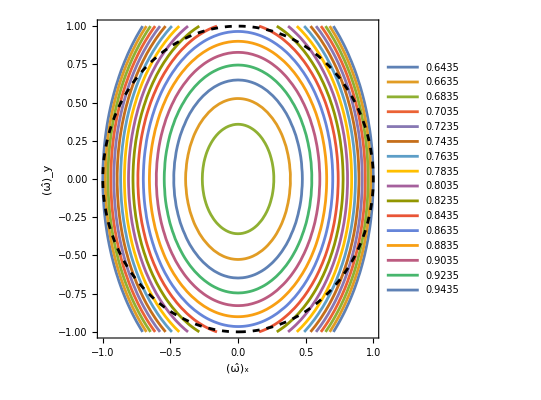

```mathematica
ihatxcurr=0.6435;
ihatycurr=0.8517;
contourstep=0.02;
contourmax=0.999;

pi1pcontours=Table[polhodeReduced[ωx,ωy,ihatxcurr,ihatycurr,pi1p]==1,{pi1p,ihatxcurr,contourmax,contourstep}];
pi1pcontourlabels=Table[pi1p,{pi1p,ihatxcurr,contourmax,contourstep}]


Show[
ContourPlot[Evaluate[pi1pcontours],{ωx,-1,1},{ωy,-1,1},PlotTheme->"Detailed",FrameLabel->{"(ω̂)_x","(ω̂)_y"},PlotLegends->pi1pcontourlabels,FrameStyle->Black],
ContourPlot[ωx^2+ωy^2==1,{ωx,-1,1},{ωy,-1,1},ContourStyle->{Dashed,Black}]
]
```